```mathematica
$Post = MatrixForm;
(*derive the projectile's position as a function of time*)
xhat = {1,0};
yhat = {0,1};
R2 = 120;
vInitial = {v0 Cos[Θ],v0 Sin[Θ]} +  r0*omega*{-Sin[omega*t0-Pi/2],Cos[omega *t0 - Pi/2]};
p = vInitial * t + {0,-r0};
startingValues = {v0 ->1, Θ->Pi/4,r0->100,t0 -> 0,omega -> .01,R->110};
path[t_] = p /. startingValues;
ThrowerExpr =  R{-Sin[omega*t-Pi/2],Cos[omega *t - Pi/2]};
Thrower[t_] = R{-Sin[omega*t-Pi/2],Cos[omega *t - Pi/2]}/.startingValues;
r = p.p;
thetaR =  R* ArcTan[xhat.p,yhat.p];
rMag[t_] = Sqrt[path[t].path[t]];
angleInRads[t_]= ArcTan[xhat.Thrower[t],yhat.Thrower[t]];
(*Define Function for projectile motion*)
gravX[t_,Θ_,v0_,x0_,g_] =v0 t Cos[θ]+x0;
gravY[t_,Θ_,v0_,y0_,g_] =-g/2*t^2 + v0 t Sin[Θ] + y0;
(*some nice helper functions*)
polarToCartesian[R_,Θ_]={R Cos[Θ],R Sin[Θ]};
rotToGrav[omega_,r_] = r/(omega^2);
cartesianToPolar[x_,y_] = {Sqrt[x^2 + y^2],ArcTan[x,y]};
(*Refactord Equations to be more general*)
(*arclength equation*)
genArcLength [t_,t0_,v0_,Θ_,r0_,omega_,R_] = {R-Sqrt[p.p],R*ArcTan[xhat.ThrowerExpr,yhat.ThrowerExpr]};
```

Null

Null

Null

«17 more identical outputs»

Null

Null

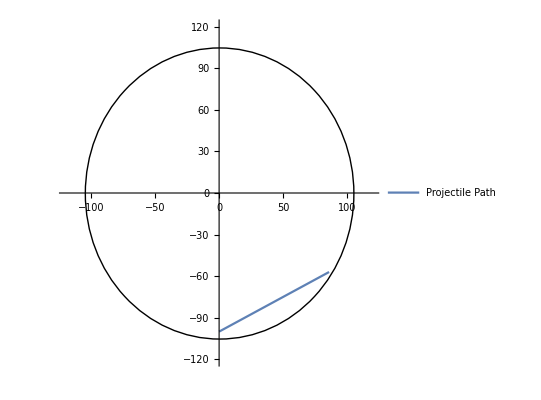

```mathematica
(*This is what our setup looks like. A ball is thrown at the bottom of the ship*)
(*Ship radius is 105, the parametric is bounded at 120 to look pretty*)
RBound = 120;
parametric = ParametricPlot[{{1,0}.path[t],{0,1}.path[t]},{t,0,43},PlotRange->{{-RBound,RBound},{-RBound,RBound}},PlotLegends->{"Projectile Path"}];
Show[ parametric,Graphics[Circle[{0,0},105]],PlotRangeClipping->True]
```

```mathematica
path[0]
```

(0.
-100.)

```mathematica
Show[%,AxesLabel->{HoldForm[Inertial X],HoldForm[Inertial Y]},PlotLabel->HoldForm[Projectile Motion on Ring World (Inertial View)],LabelStyle->{GrayLevel[0]}]
```

Show::gcomb: Could not combine the graphics objects in Show[{0.,-100.},AxesLabel→{Inertial X,Inertial Y},PlotLabel→Projectile Motion on Ring World (Inertial View),LabelStyle→{GrayLevel[0]}].

Show[{0.,-100.},AxesLabel→{Inertial X,Inertial Y},PlotLabel→Projectile Motion on Ring World (Inertial View),LabelStyle→{GrayLevel[0]}]

Null

Null

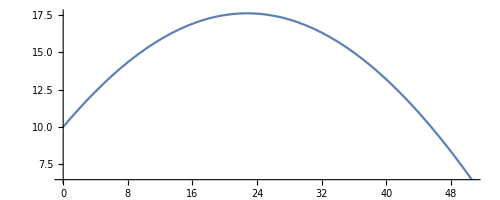

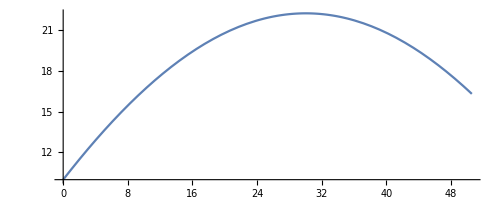

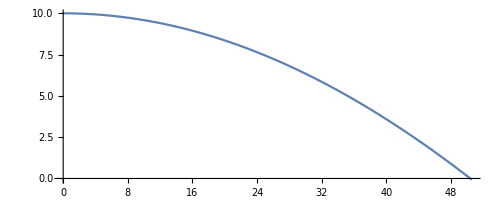

(110-√(0.171573 t^2+(-100+1.41421 t)^2)
110 ArcTan[110 Cos[0.01 t],110 Sin[0.01 t]])

-Graphics-

gravX[t,1,1,0,(t^2 (110 r0 Cos[110 t0]+v0 Cos[Θ])^2+(-r0+t (110 r0 Sin[110 t0]+v0 Sin[Θ]))^2)/12100]

```mathematica
(*pvec is a vector that points to the ball from ship center*)
(*Thus distance from center is given by*)

(*Take the x and y component of projectile and plug it into tan(x,y) to get angle. Then add or subtract relative angle of the observer*)
(*in paper, refer the arctan xy mathematica function*)
(*call it \arctan(  ,  )*)
rMag[t_] = Sqrt[path[t].path[t]];
angleInRads[t_]= ArcTan[xhat.Thrower[t],yhat.Thrower[t]];
arcLenRight = ParametricPlot[{R * angleInRads[t],R - rMag[t]}/.startingValues,{t,0,46}]
arcLenRight =  ParametricPlot[{genArcLength[t,0,1,1,100,.01,110].yhat,genArcLength[t,0,1,1,100,.01,110].xhat},{t,0,46}]
arcLenLeft =  ParametricPlot[{genArcLength[t,0,2,Pi,100,.01,110].yhat,genArcLength[t,0,2,Pi,100,.01,110].xhat},{t,0,46}]
genArcLength[t,0,2,3 Pi /4,100,.01,110]
gravPlot = ParametricPlot[{gravX[t,1,1,0,rotToGrav[110,.01]],gravY[t,1,1,-100,rotToGrav[110,.01]]},{t,0,46}]
gravX[t,1,1,0,rotToGrav[110,.01]]
```

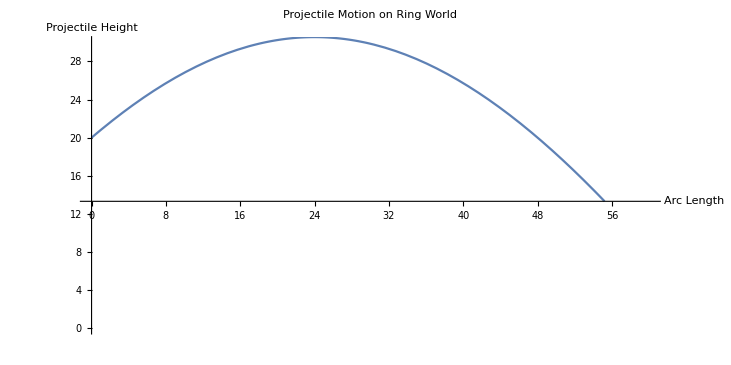

```mathematica
Show[%,AxesLabel->{HoldForm[Arc Length],HoldForm[Projectile Height]},PlotLabel->HoldForm[Projectile Motion on Ring World],LabelStyle->{GrayLevel[0]},PlotRange->{{0,60},{0,30}}]
```

```mathematica
Show[%83,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%83,ImageSize→Large]

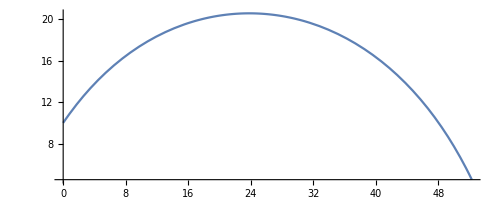

```mathematica
ParametricPlot[{110*((220. t Cos[0.01 Conjugate[t]]+110 (-110+1. t) Sin[0.01 Conjugate[t]])/(√(4. Abs[t]^2+Abs[-110+1. t]^2) √(12100 Abs[Cos[0.01 t]]^2+12100 Abs[Sin[0.01 t]]^2))),110 - rMag[t]},{t,0,45}]
```

```mathematica
Show[%285,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%285,ImageSize→Large]